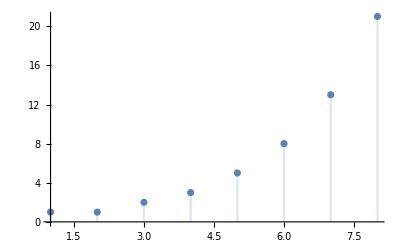

```mathematica
DiscretePlot[Evaluate[Fibonacci[n]], {n, 1, 8}]
```

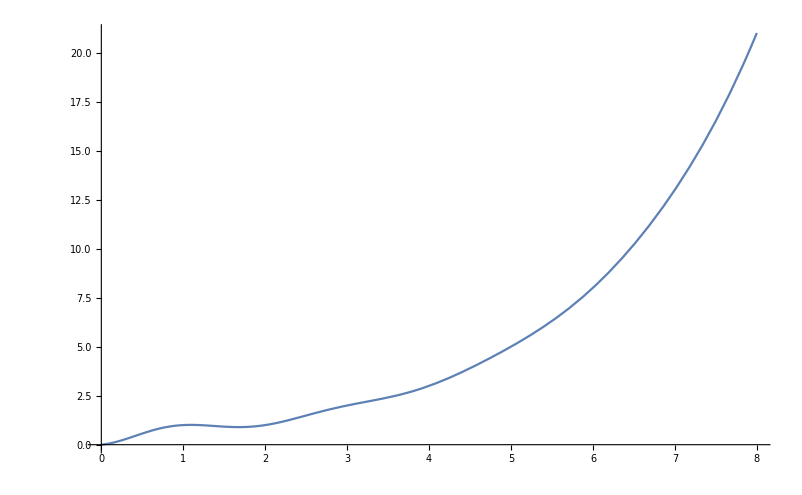

```mathematica
Plot[Fibonacci[x],{x,0,8}]
```

```mathematica
Solve[Fibonacci[n]==1/2,n]
```

```mathematica
FindRoot[Fibonacci[x]==1/2,{x,1/2}]
```

{x→0.450707}

```mathematica
root=Root[{Fibonacci[#]-1/2&,0.45070666657454406}];
```

```mathematica
ComplexPlot[Fibonacci[z],{z,-3-ⅈ,3+ⅈ},PlotLegends->Automatic]
```

-Graphics-

```mathematica
FunctionExpand[Fibonacci[1/2]]
```

√(1/10 (1+√5))

```mathematica
InverseFunction[Fibonacci]
```

```mathematica
(Fibonacci^(-1))[1/2]
```

Root-12.5Root[{-1+2 Fibonacci[#1]&,-12.5008666226388848254081765104}]-12.500866622638885

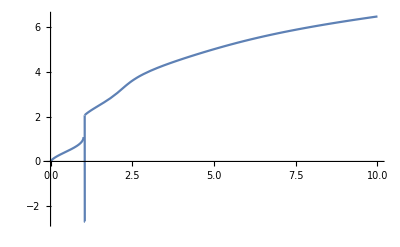

```mathematica
Plot[(Fibonacci^(-1))[x],{x,0,10}]
```

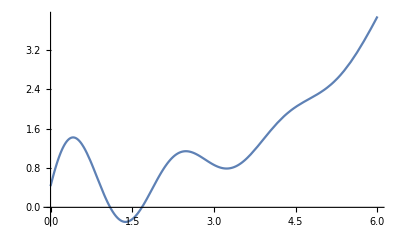

```mathematica
Plot[Evaluate@D[Fibonacci[x],x],{x,0,6}]
```

```mathematica
v1=x/.FindRoot[Evaluate@D[Fibonacci[x],x]==0,{x,1}];
root1=Root[{Evaluate@D[Fibonacci[x],x]/.x->#&,v1}]
v2=x/.FindRoot[Evaluate@D[Fibonacci[x],x]==0,{x,2}];
root2=Root[{Evaluate@D[Fibonacci[x],x]/.x->#&,v2}]
```

Root1.09Root[{(GoldenRatio^-#1 (GoldenRatio^(2 #1) Log[GoldenRatio]+Cos[π #1] Log[GoldenRatio]+π Sin[π #1]))/(√5)&,1.09457610523}]1.0945761052316456

Root1.68Root[{(GoldenRatio^-#1 (GoldenRatio^(2 #1) Log[GoldenRatio]+Cos[π #1] Log[GoldenRatio]+π Sin[π #1]))/(√5)&,1.67668837258}]1.6766883725815842

```mathematica
root2-root1
```

-Root1.09Root[{(GoldenRatio^-#1 (GoldenRatio^(2 #1) Log[GoldenRatio]+Cos[π #1] Log[GoldenRatio]+π Sin[π #1]))/(√5)&,1.09457610523}]1.0945761052316456+Root1.68Root[{(GoldenRatio^-#1 (GoldenRatio^(2 #1) Log[GoldenRatio]+Cos[π #1] Log[GoldenRatio]+π Sin[π #1]))/(√5)&,1.67668837258}]1.6766883725815842

```mathematica
Integrate[Evaluate@D[Fibonacci[x],x],{x,root1,root2}]
```

1/(√5)(-(1/2 (1+√5))^(Root1.09Root[{(GoldenRatio^(2 #1) ArcCsch[2]+ArcCsch[2] Cos[π #1]+π Sin[π #1])/(√5)&,1.09457610523}]1.0945761052316456)+(1/2 (1+√5))^(Root1.68Root[{(GoldenRatio^(2 #1) ArcCsch[2]+ArcCsch[2] Cos[π #1]+π Sin[π #1])/(√5)&,1.67668837258}]1.6766883725815842)+(2/(1+√5))^(Root1.09Root[{(GoldenRatio^(2 #1) ArcCsch[2]+ArcCsch[2] Cos[π #1]+π Sin[π #1])/(√5)&,1.09457610523}]1.0945761052316456) Cos[π Root1.09Root[{(GoldenRatio^(2 #1) ArcCsch[2]+ArcCsch[2] Cos[π #1]+π Sin[π #1])/(√5)&,1.09457610523}]1.0945761052316456]-(2/(1+√5))^(Root1.68Root[{(GoldenRatio^(2 #1) ArcCsch[2]+ArcCsch[2] Cos[π #1]+π Sin[π #1])/(√5)&,1.67668837258}]1.6766883725815842) Cos[π Root1.68Root[{(GoldenRatio^(2 #1) ArcCsch[2]+ArcCsch[2] Cos[π #1]+π Sin[π #1])/(√5)&,1.67668837258}]1.6766883725815842])

```mathematica
N[Out[121],100]
```

-0.1128779444232152079074769249432996682003711683796350189152037880741094611571312900756583449426052713

```mathematica
root2-root1//N[#,100]&
```

0.5821122673499385225145541966307266148491457421157551140183390555462910374990577746278496023012042707

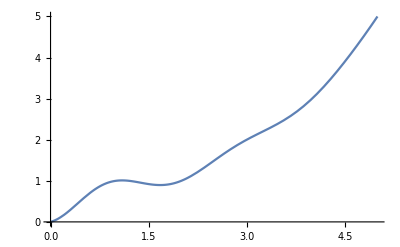

```mathematica
Plot[Fibonacci[x],{x,0,5}]
```

```mathematica
Maximize[{Fibonacci[x],0<x<3/2},x]
```

{Fibonacci[Root1.09Root[{-Log[2]+Log[1+√5]+ⅇ^(2 (Log[2]-Log[1+√5]) #1) Cos[π #1] (-Log[2]+Log[1+√5])+ⅇ^(2 (Log[2]-Log[1+√5]) #1) π Sin[π #1]&,1.0945761052316456701}]1.0945761052316456],{x→Root1.09Root[{-Log[2]+Log[1+√5]+ⅇ^(2 (Log[2]-Log[1+√5]) #1) Cos[π #1] (-Log[2]+Log[1+√5])+ⅇ^(2 (Log[2]-Log[1+√5]) #1) π Sin[π #1]&,1.0945761052316456701}]1.0945761052316456}}

```mathematica
Minimize[{Fibonacci[x],1<x<3},x]
```

{Fibonacci[Root1.68Root[{-Log[2]+Log[1+√5]+ⅇ^(2 (Log[2]-Log[1+√5]) #1) Cos[π #1] (-Log[2]+Log[1+√5])+ⅇ^(2 (Log[2]-Log[1+√5]) #1) π Sin[π #1]&,1.6766883725815841926}]1.6766883725815842],{x→Root1.68Root[{-Log[2]+Log[1+√5]+ⅇ^(2 (Log[2]-Log[1+√5]) #1) Cos[π #1] (-Log[2]+Log[1+√5])+ⅇ^(2 (Log[2]-Log[1+√5]) #1) π Sin[π #1]&,1.6766883725815841926}]1.6766883725815842}}

```mathematica
Fibonacci[x]//FunctionExpand
```

((1/2 (1+√5))^x-(2/(1+√5))^x Cos[π x])/(√5)

```mathematica
Sum[1/Fibonacci[n],{n,1,Infinity}]//{TraditionalForm@#,N@#}&
```

{1/4 √5 ((2 011/ϕ^4-4 011/ϕ^2+log(5))/(2 log(1/2 (1+√5)))+(201/ϕ^2)^2),3.35989}

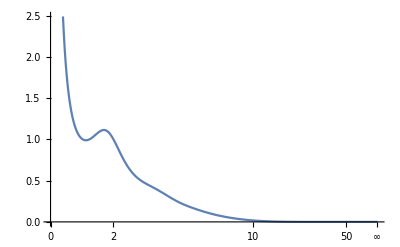

```mathematica
Plot[1/Fibonacci[x],{x,0,Infinity}]
```

```mathematica
Integrate[1/Fibonacci[x],{x,1,Infinity}]//N[#,100]&
```

2.848414230552119925891179640475217614612050016606365910732359320324076142656064854447957099796278563

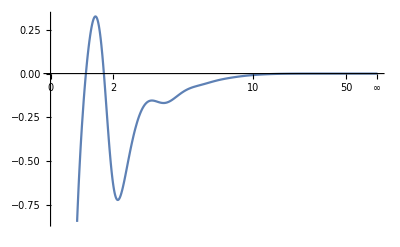

```mathematica
Plot[Evaluate@D[1/Fibonacci[x],x],{x,0,Infinity}]
```